```mathematica
vars={{},{},5,100};(*{Ds,Phis,m,tmax}*)
(*{th,tl,tlh,thl,Jh,Jl}=Sqrt[{0.1,0.1,0.05,0.05,0.1,0.1}];*)
tpar=Sqrt[{0.1,0.1,0.05,0.05,0.1,0.1}];
{kappa,gamma}={0.1,0.1};
(*Erbeta=20;beta=40*)
Er=0.1;(*10^6*ev/cm * 5nm*)
beta=0.1;(*beta=40 for Temp=0.025; for 300K*)
w0=1;
```

```mathematica
ntraj=2;
maxiter=100;
current={};
gs={0.1,1};(*Range[0.01,0.5,0.05];*)(*{0.05,0.1,0.5,1,2}*);
res={};alloutt={};
Do[
Print["================= gg = ",gg,"================="];
alloutx={};
Do[
If[Mod[itraj,5]==0,Print[" traj = ",itraj]];
out=trajectory[5,vars,gg,tpar,kappa,gamma,maxiter,False];
AppendTo[alloutx,out];
,{itraj,1,ntraj}];
AppendTo[alloutt,alloutx];
,{gg,gs}];
```

================= gg = 0.1=================

================= gg = 1=================

```mathematica
nav=1;
ntraj=50;
maxiter=500;
current={};
gs=Range[0.01,0.5,0.05];(*{0.05,0.1,0.5,1,2}*);
current={};
ig=0;
Is={};Ivsg={};Ivsg2={};Ivsg2s={};
charg={};tms={};rc={};times12={};Ivsg3={}
Do[
ig+=1;
alloutx=alloutt[[ig]];
Ix={};chargx={};Ix2={};Ix3={};
tm=0;rcx={};
Do[

{out2,Evst}=alloutx[[itraj]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[Ix,Total[charges]/tottime];


rates=out2[[All,10]];
tottime2=0;
xx=rates[[All,9;;24]];

AppendTo[Ix3,Total[charges]/Total[Gett3/@rates]];

Do[
dts=Gett3/@xx;
tottime2+=Total[dts];
,{ii,1,nav}];
tottime2=tottime2/nav;

(*If[itraj==1,times12x =Gettpm/@xx];
times12x +=Gettpm/@xx;
*)
AppendTo[rcx,Total[Total[xx]]];

AppendTo[Ix2,Total[charges]/tottime2];
AppendTo[chargx,Total[charges]];

tm +=tottime2;
,{itraj,1,ntraj}];

tm=tm/ntraj;

(*AppendTo[times12,times12x/ntraj];*)
AppendTo[rc,Total[rcx]];
AppendTo[tms,{gg,tm}];
AppendTo[Is,Ix];
AppendTo[Ivsg,{gg,Total[Ix]}];
AppendTo[Ivsg2,{gg,Total[Ix2]}];
AppendTo[Ivsg3,{gg,Total[Ix3]}];
AppendTo[Ivsg2s,Ix2];
AppendTo[charg,{gg,Total[chargx]}];
,{gg,gs}];
```

{}

Set::shape: Lists {out2,Evst} and trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False] are not the same shape.

Part::take: Cannot take positions 9 through 24 in False.

Part::pkspec1: The expression Gett3[All] cannot be used as a part specification.

Set::shape: Lists {out2,Evst} and trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False] are not the same shape.

Part::take: Cannot take positions 9 through 24 in False.

Part::pkspec1: The expression Gett3[All] cannot be used as a part specification.

Part::partw: Part 3 of {trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False],trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,«20»,«20»,0.316228,0.316228},«4»,0.1,100,False]} does not exist.

Set::shape: Lists {out2,Evst} and {trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False],trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,«2»,0.316228,0.316228},0.1,0.1,100,False]}⟦3⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::take: Cannot take positions 9 through 24 in False.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::pkspec1: The expression Gett3[All] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 4 of {trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False],trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,«20»,«20»,0.316228,0.316228},«4»,0.1,100,False]} does not exist.

Part::partw: Part 5 of {trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,0.223607,0.223607,0.316228,0.316228},0.1,0.1,100,False],trajectory[5,{{},{},5,100},0.1,{0.316228,0.316228,«20»,«20»,0.316228,0.316228},«4»,0.1,100,False]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

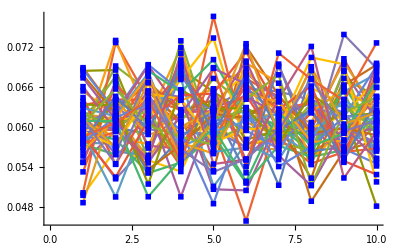

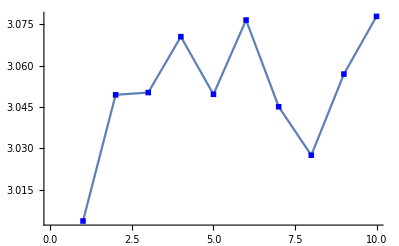

```mathematica
ListPlot[Is//Transpose,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListPlot[Total[Is//Transpose],Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

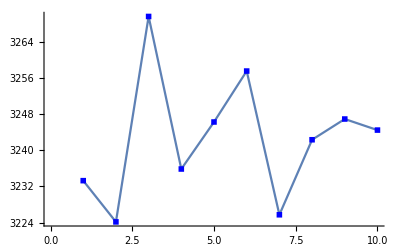

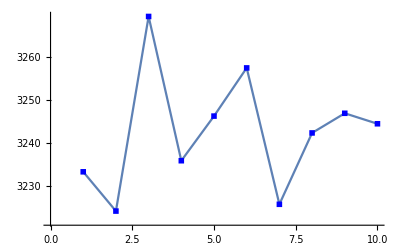

```mathematica
ListPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListLogPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

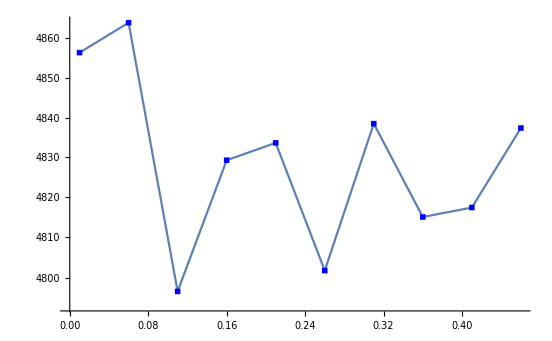

```mathematica
ListLogPlot[tms,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

```mathematica
x=Transpose[Ivsg2s];
y=Accumulate[x];
Manipulate[ListPlot[y[[i]]/i,Joined->True,PlotMarkers->{"X"}],{i,1,Length[y],1}]
```

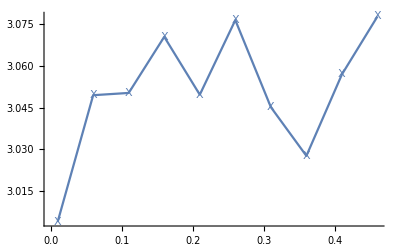

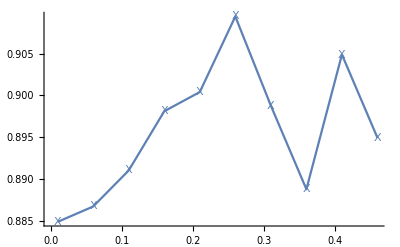

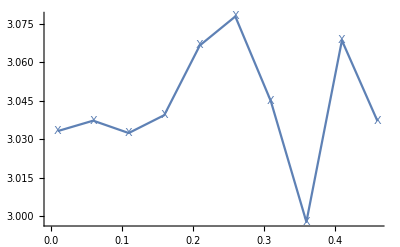

```mathematica
ListPlot[{Ivsg},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg2},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg3},Joined->True,PlotMarkers->{"X"}]
```